# Mathematica Verification of GC_WL functions

## LJ_Module.lj

argon debroglie:

```mathematica
TLJ = 2;
h = 6.62607015×10^(-34);
kB = 1.380649×10^(−23);
mkg = 39.948*1.66054*10^(-27);
ϵ = 117.05*kB ;
TK = ϵ*TLJ/kB;
Λ=h/(√(2*π*mkg*kB*TK))
σA=3.4
(Λ*10^10)/3.4
```

1.80531×10^-11

3.4

0.0530973

E_12_frac_LJ:

```mathematica
ϕ[r_,λ_,M_]:=4* (λ/M)^(1/3)(((λ/M)^(1/4)/r )^12-((λ/M)^(1/4)/r)^6  )
rList={0.0001,1.0,2.0,10.0,30.0,5.6,100000000000.0};
rListSqrt=Sqrt[rList]
```

```mathematica
{0.01,1.,1.4142135623730951,3.1622776601683795,5.477225575051661,2.3664319132398464,316227.7660168379}
phiValues=ϕ[#,3,100]&/@rListSqrt
```

{0.01,1.,1.41421,3.16228,5.47723,2.36643,316228.}

{3.35581×10^19,-0.0064247,-0.000806758,-6.45823×10^-6,-2.39195×10^-7,-0.0000367738,-6.45826×10^-36}

## Physics test: Q(N=1|V,T) test

We have the partition function  which after solving the momenta integral becomes:
  . naturally the position coordinates are in  but following Desgranges and Allen and Tildesly, we want to rescale them to a unit box for ease of simulation thuse make the change of coordinates  so that now  lives in . From this transformation we get a factor of  for each particle. And thus we get the Desgranges expression of  for N=1, there are no interactions with other particles (and in our present situation no interactions with an external field) so  thus 

 which gives us our first test of the system wide physics. For L=8  , V = 512

```mathematica
V = 8^3
Λ = 0.07509097762269842 (*for argon_deBroglie at T*=1 *)
V/Λ^3
Log[V/Λ^3]
```

512

0.075091

1.20922×10^6

14.0055

So for our first physics Test  within some monte carlo sampling error

## Q(N=2|V,T) test

Although Q(N=2) cannot be solved for directly, we can indirectly find the analytic value for it using some thermodynamic relations in the infinite/large volume limit (or we could probably just numerically integrate it with a grid or quadrature for any volume). 

	First we define the mayer f-function: .  where u(rij) is the two particle interaction potential, which for us is the Lennard jones potential. Following R.K. Pathria and Paul D. Beale’s Third edition of Statistical Mechanics (2011) Chapter 10: Statistical Mechanics of Interacting Systems page 304: we look at the second cluster integral  and switch variables to integrate over  and :  recognizing that  and switching to a shell integral and integrating over the angular terms:  (eqn 10.1.18). Now technically this integral depends on V because r12 is bounded by the finite volume of the system (which we well know in the context of this manuscript!!), but if V is large, we can assume the mayer function decays to zero before the wall is reached and thus set our bounds of integration to be 0 and infinity. For the lennard jones system this can be analytically solved:

```mathematica
(*you have to restart the notebook kernel before running this for some reason*)
int=Integrate[r^2*(Exp[-4 (1/r^12-1/r^6)]-1),{r,0,Infinity}]
```

-1/3 √(ⅇ/2) π (BesselI[-5/4,1/2]+BesselI[5/4,1/2])

```mathematica
Λ = 0.07509097762269842 (*for argon_deBroglie at T*=1 *);
b2 = (2*π)/Λ*int
```

70.7907

Now, we can examining the relation between the cluster integrals and the partition function Q by Pathria Beale equation (10.1.29):


which for the simple case of N=2 we have  or  , and taking into account the fact that  from (10.1.17) thus the general expression above becomes: 



giving us an analytic expression for Q(N=2|V,T) assuming V is large enough for the simplifications we made computing the integral of  to be valid. It is interesting to note that the periodic boundary conditions with minimum image condition of our simulation do not seem to impact the thermodynamics and give, to monte carlo/numerical error, the same result as our analytic prediction.

```mathematica
V = 8^3;
Λ = 0.07509097762269842;
QN2 = V^2/(2*Λ^6) + b2*V/Λ^3
Log[QN2]
```

7.31197×10^11

27.3179

## Ideal Gas Partition Function at high temperature limit

In the high temperature limit, our system should become the ideal gas.  The ideal gas partition can be written:



now of course because  the partition function is undefined at T=infinity thus we can expect numerical division by zero errors if we were to use T=typemax(Float64) in julia so instead we just pick a high temp and see if its close enough to ideal gas behavior.

```mathematica
TLJ = 1000000;
h = 6.62607015×10^(-34);
kB = 1.380649×10^(−23);
mkg = 39.948*1.66054*10^(-27);
ϵ = 117.05*kB ;
TK = ϵ*TLJ/kB;
Λ=h/(√(2*π*mkg*kB*TK)); (* in meters*)
σA=3.4;(*in angstroms*)
ΛLJ=(Λ*10^10)/3.4 (*thermal wavelength of argon in lennard jones units *)
```

0.000075091

```mathematica
Q[N_,V_,Λ_] := 1/(N!)(V/Λ^3)^N
Log[Q[2,8^3,ΛLJ]]
```

68.7644

```mathematica
Log[Q[3,8^3,ΛLJ]]
```

102.395

```mathematica
Log[Q[4,8^3,ΛLJ]]
```

135.737

## Reported Virial Coefficients

```mathematica
σ = 1;
B9 = -7.6*10^5*σ^24;(* at T*=1 from Table 2 Kofke 2015 10.1063/1.4927339 *)
B8 = -6.11*10^4 *σ^21;(* at T*=1 from Table 1 Kofke 2015 10.1063/1.4927339 
Kofke 2013 gives B8 = -6.4*10^4 σ^21 *)
B7 = -5.4*10^3*σ^18; (*at T*=1 from Table 2 Kofke 2013 10.1080/00268976.2012.730642*)
B6 = -580 σ^15;(*at T*=1 from Table 1 of Kofke 2013 10.1080/00268976.2012.730642*)
B5 = (-54.12)σ^12; (* at T*=1 from Table 1 of Kofke 2009 10.1080/00268970903267053*)
B4 = (-2.4623) σ^9;(* at T*=1 from Table 1 of Kofke 2009 10.1080/00268970903267053*)
B3 = 0.4297 * (2/3 π σ^3)^2;(* at T*=1 from Table 1 of Sun 1996 who uses slightly different notation than the rest 10.1021/jp9620476*)
(*crazy this one is the only positive one....*)
B2 = -2.5381 (2/3 π σ^3)^1;(* at T*=1 from Table 1 of Sun 1996 10.1021/jp9620476*)
Bs = {1,B2,B3,B4,B5,B6,B7,B8,B9}
```

{1,-5.31578,1.88488,-2.4623,-54.12,-580,-5400.,-61100.,-760000.}

```mathematica
P[ρ_,n_] := ∑_(i=1)^n Bs_⟦i⟧*ρ^i
```

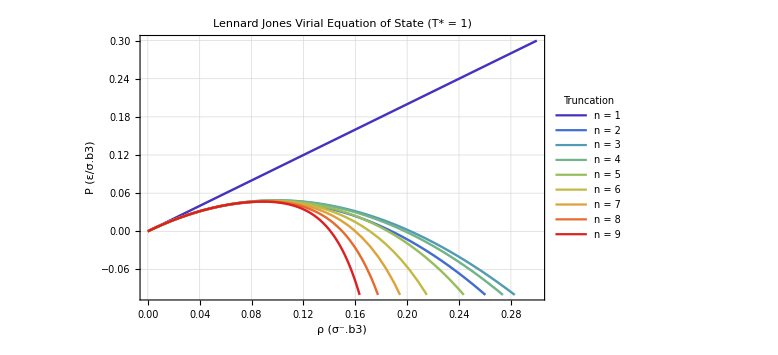

```mathematica
colors=ColorData["Rainbow"][#/9]&/@Range[1,9];

Plot[Evaluate@Table[P[ρ,n],{n,1,9}],{ρ,0,0.3},PlotStyle->(Directive[#,Thickness[0.003]]&/@colors),PlotLegends->Placed[LineLegend[colors,Table["n = "<>ToString[n],{n,1,9}],LegendLabel->"Truncation",LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->GrayLevel[0.7]]&),LabelStyle->Directive[FontFamily->"Times",FontSize->12]],After],PlotLabel->Style["Lennard Jones Virial Equation of State (T* = 1)",FontFamily->"Times",FontSize->16,Bold,Black],PlotRange->{-0.1,0.3},Frame->True,FrameLabel->{Style["ρ  (σ⁻.b3)",FontFamily->"Times",FontSize->14],Style["P  (ε/σ.b3)",FontFamily->"Times",FontSize->14]},FrameStyle->Directive[Black,Thickness[0.002]],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,Background->White,PlotRangePadding->{{0,Automatic},{Automatic,Automatic}}]
```

# Hard Sphere

Hard sphere virial coefficients are taken form sklogwiki (http://www.sklogwiki.org/SklogWiki/index.php/Hard_sphere:_virial_coefficients). To convert to partition functions, we must first convert them to irreducible integrals:
βₗ = −Bₗ₊₁ / (l + 1)
So β₁ = −B₂/2, β₂ = −B₃/3, β₃ = −B₄/4, etc. 
and then to reducible integrals (AKA cluster integrals) 
b₁ = 1
bₗ = (1/l) Σₖ₌₁ˡ⁻.b9 k βₖ bₗ₋ₖ    for l ≥ 2

and then we can go between the cluster integrals and the partition function Q either  by Pathria Beale equation (10.1.29):



or via Ushcat’s recursion relation for the configuration integral Z (which he calls Q) via his equation (6) in 10.1103/PhysRevE.98.032135 :

```mathematica
(*this data is from sklogwiki http://www.sklogwiki.org/SklogWiki/index.php/Hard_sphere:_virial_coefficients *)
B2 = 4
Bs = {B2, 0.625*(B2^2),0.2869495*(B2^3), 0.110252*(B2^4), 0.03888198*(B2^5), 0.01302354*(B2^6),0.0041832*(B2^7), 0.0013094*(B2^8), 0.0004035*(B2^9), 0.000122*(B2^10), 0.000027*(B2^11)  }
```

Virial coefficients Bn (in units of Vsphere^(n-1)):

B2 = 1

B3 = 2.5

B4 = 4.59119

B5 = 7.05613

B6 = 9.95379

B7 = 13.3361

B8 = 17.1344

B9 = 21.4532

B10 = 26.4438

B11 = 31.9816

B12 = 28.3116

Irreducible cluster integrals β_l:

β_1 = -1/2

β_2 = -0.833333

β_3 = -1.1478

β_4 = -1.41123

β_5 = -1.65896

β_6 = -1.90516

β_7 = -2.1418

β_8 = -2.38369

β_9 = -2.64438

β_10 = -2.90742

Reducible (Mayer) cluster integrals b_l:

b_1 = 1

b_2 = -1/4

b_3 = -5.1388889×10^-1

b_4 = -6.9244572×10^-1

b_5 = -7.1627094×10^-1

b_6 = -6.0031032×10^-1

b_7 = -3.6829754×10^-1

b_8 = -3.9046735×10^-2

b_9 = 3.3781326×10^-1

b_10 = 7.082218×10^-1

b_11 = 1.0473012

ln Q(N,V,T) = ln Z_N - ln N! - 3N ln λ:

N = 1:  ln Q = 8.9872

N = 2:  ln Q = 16.5881

N = 3:  ln Q = 23.378

N = 4:  ln Q = 29.5925

N = 5:  ln Q = 35.3607

N = 6:  ln Q = 40.7642

N = 7:  ln Q = 45.8594

N = 8:  ln Q = 50.6875

N = 9:  ln Q = 55.2799

N = 10:  ln Q = 59.6617

N = 11:  ln Q = 63.8527

N = 12:  ln Q = 67.8698

N = 13:  ln Q = 71.7267

N = 14:  ln Q = 75.4353

N = 15:  ln Q = 79.006

N = 16:  ln Q = 82.4475

N = 17:  ln Q = 85.7677

N = 18:  ln Q = 88.9736

N = 19:  ln Q = 92.0714

N = 20:  ln Q = 95.0665

Verification: Bn recovered from β_l:

B2 : input = 1  recovered = 1

B3 : input = 2.5  recovered = 2.5

B4 : input = 4.59119  recovered = 4.59119

B5 : input = 7.05613  recovered = 7.05613

B6 : input = 9.95379  recovered = 9.95379

B7 : input = 13.3361  recovered = 13.3361

B8 : input = 17.1344  recovered = 17.1344

B9 : input = 21.4532  recovered = 21.4532

B10 : input = 26.4438  recovered = 26.4438

B11 : input = 31.9816  recovered = 31.9816

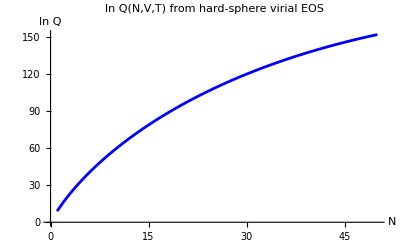

```mathematica
(*Hard Sphere Virial Coefficients to Partition Functions*)
ClearAll["Global`*"]

(*Virial coefficients from SklogWiki*)
(*B2 through B4 are exact;B5 through B12 are numerical*)
(*Expressed as Bn/B2^(n-1),where B2=b=(2/3)π σ^3*)
(*Here we use Bn/Vsphere^(n-1) where Vsphere=π/6 σ^3*)
(*so B2=4 Vsphere*)

B2reduced=4;

(*Reduced virial coefficients Bn/B2^(n-1)*)
BnOverB2nm1={1,(*B2*)0.625,(*B3=5/8*)0.28694950,(*B4*)0.11025210,(*B5*)0.03888198,(*B6*)0.01302354,(*B7*)0.0041832,(*B8*)0.0013094,(*B9*)0.0004035,(*B10*)0.000122,(*B11*)0.000027            (*B12*)};

nMax=Length[BnOverB2nm1];

(*Construct actual Bn in units of Vsphere^(n-1)*)
Bn=Table[BnOverB2nm1[[n]]*B2reduced^(n-1),{n,1,nMax}];

Print["Virial coefficients Bn (in units of Vsphere^(n-1)):"]
Do[Print["  B",n+1," = ",Bn[[n]]],{n,1,nMax}];

(* =====================*)
(*Step 1:Bn->β_l*)
(* =====================*)

(*β[l]=-B[l+1]/(l+1) (Pathria eq.10.4.22)*)
β=Table[-Bn[[l]]/(l+1),{l,1,nMax-1}];

Print["\nIrreducible cluster integrals β_l:"]
Do[Print["  β_",l," = ",β[[l]]],{l,1,Length[β]}];

(* =====================*)
(*Step 2:β_l->b_l*)
(* =====================*)

(*Recursion:b[l]=(1/l) Sum[k β[k] b[l-k],{k,1,l-1}]*)
(*with b[1]=1*)

bCluster=ConstantArray[0.0,nMax];
bCluster[[1]]=1;

Do[bCluster[[l]]=(1/l) Sum[k β[[k]] bCluster[[l-k]],{k,1,Min[l-1,Length[β]]}];,{l,2,nMax}];

Print["\nReducible (Mayer) cluster integrals b_l:"]
Do[Print["  b_",l," = ",ScientificForm[bCluster[[l]],8]],{l,1,nMax}];


(*Step 3:Ushcats recursion for Z_N*)configIntegral[Nmax_Integer,V_,bList_List]:=Module[{Z=ConstantArray[0,Nmax+1],nCluster},nCluster=Length[bList];
Z[[1]]=1;
Do[Z[[i+1]]=(V/i) Sum[n bList[[n]] Z[[i-n+1]],{n,1,Min[i,nCluster]}];,{i,1,Nmax}];
Z[[2;;]]]

(*Set physical parameters*)
σ=1.0;
Vsphere=π/6 σ^3;
λ=1.0;  (*thermal de Broglie wavelength-set to match your simulation*)
boxL=20.0;
V=boxL^3;

bClusterAbs=Table[bCluster[[l]]*Vsphere^(l-1),{l,1,nMax}];

Nparticles=50;

ZN=configIntegral[Nparticles,V,bClusterAbs];

(*Full partition function:Q(N,V,T)=Z_N/(N! λ^(3N))*)
(*ln Q(N)=ln Z_N-ln N!-3N ln λ*)
lnQ=Table[Log[ZN[[i]]]-LogGamma[i+1]-3 i Log[λ],{i,1,Nparticles}];

Print["\nln Q(N,V,T) = ln Z_N - ln N! - 3N ln λ:"]
Do[Print["  N = ",i,":  ln Q = ",lnQ[[i]]],{i,1,Min[20,Nparticles]}];

(*Verification*)
Print["\nVerification: Bn recovered from β_l:"]
Do[BnRecovered=-(l+1) β[[l]];
Print["  B",l+1," : input = ",Bn[[l]],"  recovered = ",BnRecovered],{l,1,Length[β]}];

(*Convenience function*)
lnQFromBn[BnList_List,Vbox_,Nmax_Integer,λval_]:=Module[{nB,βloc,bloc,Zloc},nB=Length[BnList];
βloc=Table[-BnList[[l]]/(l+1),{l,1,nB-1}];
bloc=ConstantArray[0.0,nB];
bloc[[1]]=1;
Do[bloc[[l]]=(1/l) Sum[k βloc[[k]] bloc[[l-k]],{k,1,Min[l-1,Length[βloc]]}];,{l,2,nB}];
Zloc=configIntegral[Nmax,Vbox,bloc];
Table[Log[Zloc[[i]]]-LogGamma[i+1]-3 i Log[λval],{i,1,Nmax}]]

(*Plot*)
ListPlot[Transpose[{Range[Nparticles],lnQ}],PlotLabel->"ln Q(N,V,T) from hard-sphere virial EOS",AxesLabel->{"N","ln Q"},PlotStyle->{Blue,PointSize[0.015]},Joined->True,PlotRange->All]
```